Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos. 
F. Javier Muñoz Delgado

## Tema 6. Integrales. Problemas de examen.

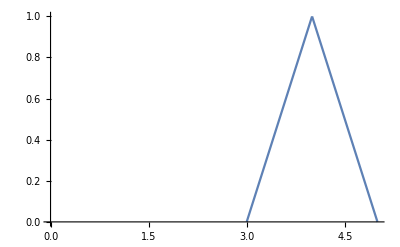
## 1. Calcular el volumen del cuerpo obtenido al girar la gráfica de la función f(x) = Piecewise[{{x-3, 3<=x<=4}, {5-x, 4<=x<=5}}] respecto al eje horizontal. -Graphics- El sexto decimal es: A) 5, B) 7, C) 9, D) 1, E) 3 El sexto decimal es: A) 1, B) 3, C) 5, D) 7, E) 9 El segundo decimal es: A) 3, B) 5, C) 7, D) 9, E) 1 El segundo decimal es: A) 7, B) 9, C) 1, D) 3, E) 5 Julio 24. Aula de Informática

Solución:
El volumen que se obtiene al girar la gráfica de una función f(x), en un intervalo [a,b], alrededor del eje horizontal es ∫_a^b π f^2(x)ⅆxes

```mathematica
ParametricPlot3D[{x,Which[x<4,x-3,True,5-x] Cos[t],Which[x<4,x-3,True,5-x] Sin[t]},{x,3,5},{t,0,2Pi}]
```

-Graphics3D-

```mathematica
∫_3^5 π (Which[x<4,x-3,True,5-x])^2 ⅆx
```

(2 π)/3

```mathematica
N[(2 π)/3,20]
```

2.0943951023931954923

El sexto decimal es 5.
El segundo decimal es 9.

## 1. Calcular el volumen del cuerpo obtenido al girar la gráfica de la función f(x) = Piecewise[{{x-3, 3<=x<=4}, {5-x, 4<=x<=5}}] respecto al eje vertical. -Graphics- -Graphics3D- El noveno decimal es: 1) 1, 2) 3, 3) 5, 4) 8, 5) 6 El segundo decimal es: 1) 1, 2) 3, 3) 5, 4) 8, 5) 6 Enero 24. Aula de Informática

Solución: Siguiendo lo visto en el tema de integrales, el volumen del sólido de revolución al girar la gráfica de una función f(x) en un intervalo [a,b] alrededor del eje vertical es ∫_a^b 2 π x f(x)ⅆx.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:=Which[3<=x<=4,x-3,4<=x<=5,5-x]
```

```mathematica
N[∫_3^5 (2π x f[x] )ⅆx,15]
```

25.1327412287183

El noveno decimal es el 8.
El segundo decimal es el 3.

## 1.- Calcular el área de la superficie obtenida al girar la gráfica de la función f(x)= √(1+x) - 1 con x en [0,2] alrededor del eje horizontal. -Graphics3D- Superficie (4 cifras decimales): Enero 19. Aula de Informática

Solución:
Siguiendo lo estudiado en prácticas de Integrales definidas y aplicaciones, el área se obtiene calculando la integral ∫_a^b 2π f(x)√(1+f'(x)^2)ⅆx

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=√(1+x)-1
```

```mathematica
∫_0^2 (2 π f[x] √(1+f'[x]^2) )ⅆx
```

1/6 π (√5+13 √13-6 √39+3 ArcSinh[2]-3 ArcSinh[2 √3])

```mathematica
N[%]
```

5.28925

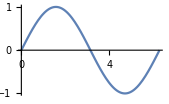
## 1.- Calcular la longitud de la gráfica de la función f(x) = sen x, con x en [0,2π] . -Graphics- Longitud (4 cifras decimales): Enero 19. Aula de Informática

Solución:
Siguiendo la Práctica de Integrales definidas y aplicaciones, la longitud se obtiene calculando la integral ∫_0^(2π) √(1+(f' [x])^2)ⅆx:

```mathematica
f[x_]:=Sin[x]
```

```mathematica
∫_0^(2π) √(1+(f' [x])^2)ⅆx
```

4 √2 EllipticE[1/2]

```mathematica
N[%]
```

7.6404

## 1.- Calcular el volumen obtenido al girar la gráfica de la función f(x)= 4-2x, con x en [0,2] alrededor del eje vertical y limitado por el plano horizontal. Volumen: -Graphics3D- Enero 19. Aula de Informática

Solución: 
Siguiendo la práctica de Integrales definidas y aplicaciones, el volumen se obtiene calculando la integral

```mathematica
∫_0^2 (2 π x  (4-2x))ⅆx
```

(16 π)/3

```mathematica
N[%]
```

16.7552

También podría razonarse que como el cuerpo obtenido es un cono, su volumen es 1/3 del área de la base (π por el radio al cuadrado) por la altura: 
1/3 (π 2^2)*4= 16 π/3.

## Sea tu DNI: AB.CDE.FGH, M = MÁXIMO {A, B, C, D, E, F, G, H} = ___, N = MIN {A, B, C, D, E, F, G, H, I}= ____ 1.- Calcular el volumen obtenido al girar la gráfica de la función f(x)= G+2+ sen (πx) con x en [N,M] alrededor del eje vertical y limitado por el plano horizontal. Volumen: -Graphics3D- Julio 18. Aula de Informática

Solución:
Siguiendo lo explicado en la Práctica sobre aplicaciones de las integrales definidas, tenemos

```mathematica
∫_n^m 2 π x(g+2+Sin[Pi x])ⅆx//Simplify
```

2 m^2 π+g m^2 π-2 n^2 π-g n^2 π+(2 (-m π Cos[m π]+n π Cos[n π]+Sin[m π]-Sin[n π]))/π

## 1.- Calcular el volumen obtenido al girar la gráfica de la función f(x)= 2+ sen (π x) con x en [0,3] alrededor del eje horizontal. -Graphics3D- Volumen: Enero 18. Aula de informática

Solución:
Siguiendo la Práctica de Integrales vemos que el volumen obtenido al girar respecto al eje horizontal OX es la integral ∫_a^b π f^2(x)ⅆx. En este caso,

```mathematica
∫_0^3 π (2+Sin[π x])^2 ⅆx
```

8+(27 π)/2

```mathematica
N[%]
```

50.4115

## 6.- Supongamos que la función f(t) aproxima el número de habitantes que tiene una población para cada tiempo t , medido en meses, con t en [0,60], y que el crecimiento de esta población viene dado por la siguiente expresión: f ‘(t) = 400 + 30 √t a) Si la población en la actualidad, t=0, es de 90 000 habitantes, ¿Cuál será la población dentro de 9 meses? b) Calcular ∫_9^16 f'(t)ⅆt e interpretar el resultado. Julio 24.

Solución:
Conocida la derivada de la función f(t), podemos calcular la función f(t) mediante integración:
∫f'(t)ⅆt=∫(400+30 √t)ⅆt = ∫(400+30 t^(1/2))ⅆt = 400 t +(30 t^(3/2))/(3/2) + C= 400 t +20 t^(3/2) + C 
De todas las funciones primitivas, buscamos aquella que en t=0 vale 90 000. Para ello es fácil ver que C debe ser igual a 90000.
f(t)=400 t +20 t^(3/2) + 90000

a) La población dentro de 9 meses será:
f(9)=400 *9 +20*9^(3/2) + 90000= 3600+20*3^3+90000 = 3600+20*27+90000=3600+540+90000=94140

b) Calculamos la integral: ∫_9^16 f'(t)ⅆt=∫_9^16 (400+30 √t)ⅆt=∫_9^16 (400+30 t^(1/2))ⅆt=(400 t +(30 t^(3/2))/(3/2))|t=16
t=9=(400 t +20 t^(3/2))|t=16
t=9=(400 *16 +20 16^(3/2))-(400 9 +20 9^(3/2))=(400 *16 +20 4^3)-(400 9 +20 3^3)=(6400  +20 *64)-(3600 +20*27) =(6400  +1280)-(3600 +540) =2800  +740=3540 
Significaría que el crecimiento de la población entre los 9 y los 16 meses es de 3540 personas.

También se podría escribir ∫_9^16 f'(t)ⅆt=f(16)-f(9) = (400 *16 +20 16^(3/2)+90000)-(400 9 +20 9^(3/2)+90000)=(400 *16 +20 4^3)-(400 9 +20 3^3)=(6400  +20 *64)-(3600 +20*27) =(6400  +1280)-(3600 +540) =2800  +740=3540 

Con el Mathematica:

```mathematica
g[t_]:=400 + 30 √t
```

```mathematica
∫g[t]ⅆt
```

400 t+20 t^(3/2)

```mathematica
f[t_]:=400 t+20 t^(3/2)+90000
```

```mathematica
f[9]
```

94140

```mathematica
∫_9^16 g[t]ⅆt
```

3540